```mathematica
Remove[x]
```

```mathematica
sol1=NDSolve[{x'[t]==x[t](1-x[t]/180.),x[0]==10},x,{t,0,50}]
```

{{x→InterpolatingFunction[…]}}

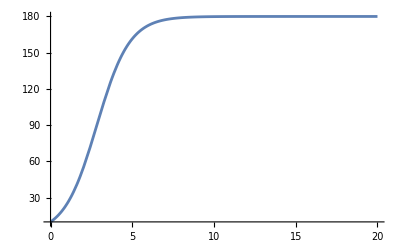

```mathematica
g1=Plot[Evaluate[{x[t]}/. First[sol1]],{t,0,20},PlotRange->All]
```

```mathematica
Remove[y]
```

```mathematica
sol2=NDSolve[{y'[t]==y[t](1-y[t-1]/180.),y[t/;t<=0]==10.},y,{t,-1,50}]
```

{{y→InterpolatingFunction[…]}}

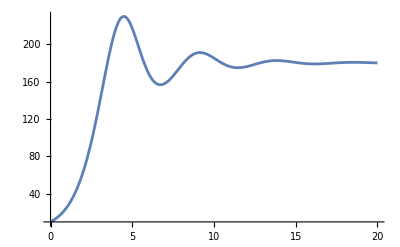

```mathematica
g2=Plot[Evaluate[{y[t]}/. First[sol2]],{t,0,20},PlotRange->All]
```

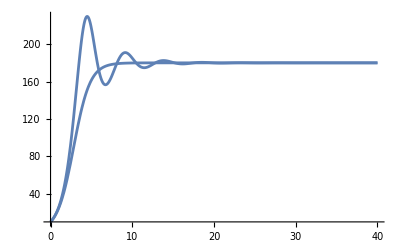

```mathematica
Show[g1,g2]
```

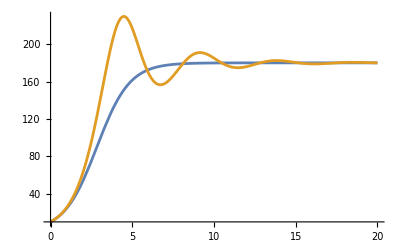

```mathematica
Plot[Evaluate[{{x[t]}/. First[sol1],{y[t]}/. First[sol2]}],{t,0,20},PlotRange->All]
```